{0}

```mathematica
fireProg={Table[20 i,{i,0,9}],{1,84,543,1521,3100,5298,7893,11100,14667,18628}/(710*760)}ᵀ;
```

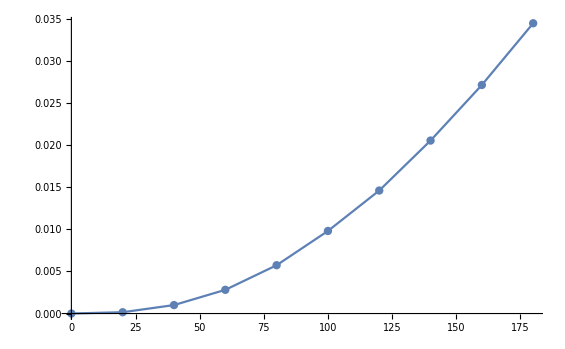

```mathematica
ListPlot[fireProg,Joined->True,Mesh->All]
```

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, … . 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

```mathematica
710*760
```

539600

```mathematica
interpolation = Interpolation[fireProg];
```

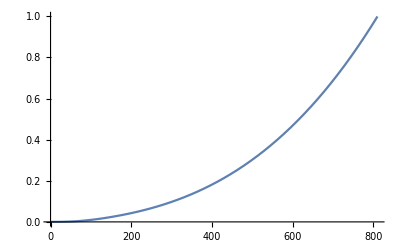

```mathematica
Plot[interpolation[x],{x,0,60.* 13.5}]
```

```mathematica
interpolation[60.* 12.4]
```

InterpolatingFunction::dmval: Input value {744.} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.803306

```mathematica
710 * 760 *.8
```

431680.

```mathematica
b=((.005)^5/(.25))^(1/4);
a=((.005)/b)^(1/2);
f[x_]:=b a^x;
InverseFunction[f][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

2.04498 Log[531.83 x]

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

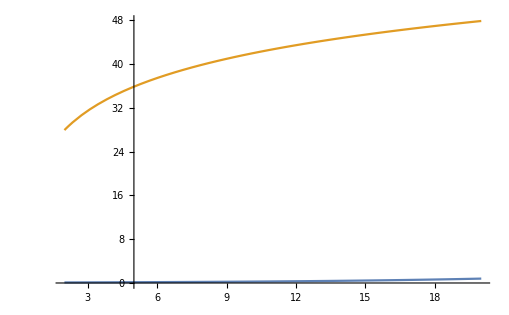

```mathematica
Plot[f[x],{x,2,20}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

General::stop: Further output of InverseFunction :: ifun will be suppressed during this calculation.

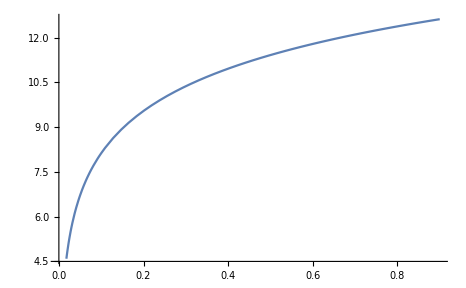

```mathematica
Plot[InverseFunction[f][y],{y,0,.9}]
```